In this notebook we will be calculating the dimensionless funcitons R_≫ and R_≪

```mathematica
SetDirectory[NotebookDirectory[]];
sawSpecDictLL=Import["N-Specs/sawSpecsLL.m"];
boxSpecDictLL=Import["N-Specs/boxSpecsLL.m"];
sawSpecDictGG=Import["N-Specs/sawSpecsGG.m"];
boxSpecDictGG=Import["N-Specs/boxSpecsGG.m"];

(* In defining the sepctra we normalized the neutrino spectrum to integrate to 1, and scaled out  α d^2 Z^2 from the cross section *) 
ΦνSolarForMuOnly= 1.2693788196538383*10^10;
ΦνSolar= 6.538802954197485*10^10
dRef=1.97 10^-9(* MeV^-1 *) 197 (* MeV fm *) 10^-13(* fm per cm  *);
Zref=12;
overallNormalization= α ΦνSolarForMuOnly dRef^2 10^30/.α-> 1/137;
VnARef=10^30;
overallNormalization
```

6.5388×10^10

0.139552

```mathematica
Γ=(d^2 mN^3)/(4π);
decEqRadEarth= Assuming[{mN>0,d>0},d/.Solve[197/Γ==6.4 10^3* 10^18 ,d]⟦2⟧//Quiet](* fm per km*)
```

(6.21939×10^-10)/mN^(3/2)

## Small Decay Length

```mathematica
sawInterpLL=<||>;
boxInterpLL=<||>;
Do[sawInterpLL[mN]=Interpolation@(sawSpecDictLL[mN]),{mN,Keys@sawSpecDictLL}];
Do[boxInterpLL[mN]=Interpolation@(boxSpecDictLL[mN]),{mN,Keys@boxSpecDictLL}];
```

```mathematica
binRatesSawLL=<||>;
binRatesBoxLL=<||>;
Do[binRatesSawLL[mN]=<|"borLERI"-> NIntegrate[sawInterpLL[mN][x],{x,0.2,0.8}],"borLERII"-> NIntegrate[sawInterpLL[mN][x],{x,0.8,2.5}],"borHER"-> NIntegrate[sawInterpLL[mN][x],{x,2,15}],"SK"-> NIntegrate[sawInterpLL[mN][x],{x,4.49,15.5}]|>,{mN,Keys@sawInterpLL}];
Do[binRatesBoxLL[mN]=<|"borLERI"-> NIntegrate[boxInterpLL[mN][x],{x,0.2,0.8}],"borLERII"-> NIntegrate[boxInterpLL[mN][x],{x,0.8,2.5}],
"borHER"-> NIntegrate[boxInterpLL[mN][x],{x,2,15}],
"SK"-> NIntegrate[boxInterpLL[mN][x],{x,4.49,15.5}]|>,{mN,Keys@boxInterpLL}];
```

## Long Decay Length

```mathematica
sawInterpGG=<||>;
boxInterpGG=<||>;
Do[sawInterpGG[mN]=Interpolation@(sawSpecDictGG[mN]),{mN,Keys@sawSpecDictGG}];
Do[boxInterpGG[mN]=Interpolation@(boxSpecDictGG[mN]),{mN,Keys@boxSpecDictGG}];
```

```mathematica
binRatesSawGG=<||>;
binRatesBoxGG=<||>;
Do[binRatesSawGG[mN]=<|"borLERI"-> NIntegrate[sawInterpGG[mN][x],{x,0.2,0.8}],"borLERII"-> NIntegrate[sawInterpGG[mN][x],{x,0.8,2.5}],"borHER"-> NIntegrate[sawInterpGG[mN][x],{x,2,15}],"SK"-> NIntegrate[sawInterpGG[mN][x],{x,4.49,15.5}]|>,{mN,Keys@sawInterpGG}];
Do[binRatesBoxGG[mN]=<|"borLERI"-> NIntegrate[boxInterpGG[mN][x],{x,0.01,0.8}],"borLERII"-> NIntegrate[boxInterpGG[mN][x],{x,0.8,2.5}],"borHER"-> NIntegrate[boxInterpGG[mN][x],{x,2,15}],"SK"-> NIntegrate[boxInterpGG[mN][x],{x,4.49,15.5}]|>,{mN,Keys@boxInterpGG}];
```

## Rate Curves

OVERALL NORMALIZATION IS INCLUDED IN THIS CELL

```mathematica
RfuncBinnedLL=<||>;
RfuncBinnedGG=<||>;
RfuncBinned=<||>;
makeRateCurve[listName_,exptStr_]:= Interpolation[(# UnitStep[#]&)/@Table[{mN,overallNormalization listName[mN][exptStr]},{mN,Keys@listName}],InterpolationOrder->1];
exptNames={"borLERI","borLERII","borHER","SK"};
```

Small Decay length

```mathematica
RfuncBinnedSaw=<||>;
Do[
RfuncBinnedSaw[exptStr]=makeRateCurve[binRatesSawLL,exptStr],{exptStr,exptNames}]

RfuncBinnedBox=<||>;
Do[
RfuncBinnedBox[exptStr]=makeRateCurve[binRatesBoxLL,exptStr],{exptStr,exptNames}]

RfuncBinnedLL["Saw"]=RfuncBinnedSaw;
RfuncBinnedLL["Box"]=RfuncBinnedBox;
```

Large Decay Length

```mathematica
RfuncBinnedSaw=<||>;
Do[
RfuncBinnedSaw[exptStr]=makeRateCurve[binRatesSawGG,exptStr],{exptStr,exptNames}]

RfuncBinnedBox=<||>;
Do[
RfuncBinnedBox[exptStr]=makeRateCurve[binRatesBoxGG,exptStr],{exptStr,exptNames}]

RfuncBinnedGG["Saw"]=RfuncBinnedSaw;
RfuncBinnedGG["Box"]=RfuncBinnedBox;
```

Combined together in one dictionary

```mathematica
RfuncBinned["LL"]=RfuncBinnedLL;
RfuncBinned["GG"]=RfuncBinnedGG;
```

## Saw

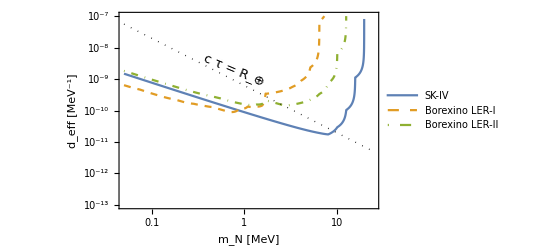

```mathematica
(* Borexino  *)
numSecInDay=60 60 24;
densityLiqSint=876 (* kg/m3*)*  0.001 (* tonne/kg*) /10^6 (* cm^3/m^3*)//N ;(* from http://borex.lngs.infn.it/Thesis/M.Leung_PhD_Thesis.pdf*) 
fidVol=100 (*tonne*) / densityLiqSint;
nA=1.01 10^23(* cm *);
Zeff=11.8;
LERIrate=60;
LERIIrate=17;
LofTAvBXNO=Mean[Import["Earth-Geo/L-avg-Borexino.m"]]⟦2⟧;

dLLExclLERI=1.97 10^-9(LERIrate/((104 ) numSecInDay)  (10^30/(nA fidVol))(12/Zeff)^2 (1/(1/2 RfuncBinned["LL"]["Saw"]["borLERI"][mN]+10^-32))  )^(1/2)HeavisideTheta[RfuncBinned["LL"]["Saw"]["borLERI"][mN]+0.00001];
dLLExclLERII=1.97 10^-9(LERIIrate/((104 ) numSecInDay)  (10^30/(nA fidVol))(12/Zeff)^2 (1/(1/2 RfuncBinned["LL"]["Saw"]["borLERII"][mN]+10^-32)) )^(1/2)HeavisideTheta[RfuncBinned["LL"]["Saw"]["borLERII"][mN]+0.00001];
dGGExclLERI=1.97 10^-9( LERIrate/(2 (104 ) numSecInDay)  (10^30/(nA fidVol))(12/Zeff)^2(1/mN^4 1/LofTAvBXNO 1/(RfuncBinned["GG"]["Saw"]["borLERI"][mN]+10^-32)))^(1/4)HeavisideTheta[RfuncBinned["GG"]["Saw"]["borLERI"][mN]+0.00001];
dGGExclLERII=1.97 10^-9(LERIIrate/(2 (104 ) numSecInDay)  (10^30/(nA fidVol))(12/Zeff)^2 (1/mN^4 1/LofTAvBXNO 1/(RfuncBinned["GG"]["Saw"]["borLERII"][mN]+10^-32)))^(1/4);

(* SK*)
numSecInDay=60 60 24;
densityH20=1 (* g/cm3*)*  0.001 (* tonne/kg*) 0.001 (* kg/g*)//N ;(* from http://borex.lngs.infn.it/Thesis/M.Leung_PhD_Thesis.pdf*) 
fidVolSK=22.5 10^3 (*tonne*) / densityH20;
nA=1.01 10^23(* cm *);
Zeff=11.8;
LofTAvSK=Mean[Import["Earth-Geo/L-avg-SK.m"]]⟦2⟧;
rateBoundSK=4.62;
dLLExclSK=1.97 10^-9(rateBoundSK/((104 ) numSecInDay)  (10^30/(nA fidVolSK))(12/Zeff)^2 (1/(1/2 RfuncBinned["LL"]["Saw"]["SK"][mN]+10^-32)) )^(1/2) HeavisideTheta[RfuncBinned["LL"]["Saw"]["borLERII"][mN]+0.00001];
dGGExclSK=1.97 10^-9( rateBoundSK/(2 (104 ) numSecInDay)  (10^30/(nA fidVolSK))(12/Zeff)^2(1/mN^4 1/LofTAvSK 1/(RfuncBinned["GG"]["Saw"]["SK"][mN]+10^-32)))^(1/4)HeavisideTheta[RfuncBinned["GG"]["Saw"]["SK"][mN]+0.00001];
LogLogPlot[{Max[dLLExclSK,dGGExclSK],Max[dLLExclLERI,dGGExclLERI],Max[dLLExclLERII,dGGExclLERII],decEqRadEarth},{mN,0.05,25},PlotRange->{10^-13,10^-7},Frame-> True,FrameStyle->Black,PlotStyle->{Automatic,Dashed,DotDashed,{Dotted,Thick,Black}},
Epilog->{Inset[Rotate[Style["c τ = R_⊕",13],-0.4],{-0.25,-20.0}]},PlotLegends->Placed[{"SK-IV","Borexino LER-I","Borexino LER-II"},{0.3,0.175}],FrameLabel->(Style[#,14]&)/@{"m_N   [MeV]","d_eff    [MeV^-1]"},PlotRangePadding->0]//Quiet
Export["Guess-Curves/BRXNO-LERI-SAW.m",1/(1.97 10^-9)Max[dGGExclLERI,dLLExclLERI]];
Export["Guess-Curves/BRXNO-LERII-SAW.m",1/(1.97 10^-9)Max[dGGExclLERII,dLLExclLERII]];
Export["Guess-Curves/BRXNO-SK-SAW.m",1/(1.97 10^-9)Max[dGGExclSK,dLLExclSK]];
```

## Box

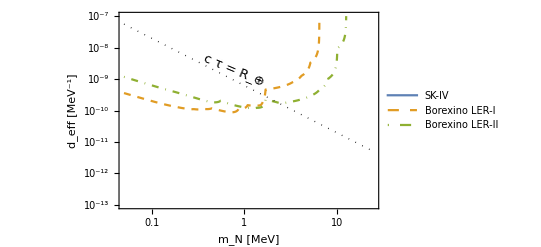

```mathematica
(* Borexino  *)
numSecInDay=60 60 24;
densityLiqSint=876 (* kg/m3*)*  0.001 (* tonne/kg*) /10^6 (* cm^3/m^3*)//N ;(* from http://borex.lngs.infn.it/Thesis/M.Leung_PhD_Thesis.pdf*) 
fidVol=100 (*tonne*) / densityLiqSint;
nA=1.01 10^23(* cm *);
Zeff=11.8;
LERIrate=60;
LERIIrate=17;
LofTAvBXNO=Mean[Import["Earth-Geo/L-avg-Borexino.m"]]⟦2⟧;

dLLExclLERI=1.97 10^-9(LERIrate/((104 ) numSecInDay)  (10^30/(nA fidVol))(12/Zeff)^2 (1/(1/2 RfuncBinned["LL"]["Box"]["borLERI"][mN]+10^-32))  )^(1/2)HeavisideTheta[RfuncBinned["LL"]["Box"]["borLERI"][mN]+0.00001];
dLLExclLERII=1.97 10^-9(LERIIrate/((104 ) numSecInDay)  (10^30/(nA fidVol))(12/Zeff)^2 (1/(1/2 RfuncBinned["LL"]["Box"]["borLERII"][mN]+10^-32)) )^(1/2)HeavisideTheta[RfuncBinned["LL"]["Box"]["borLERII"][mN]+0.00001];
dGGExclLERI=1.97 10^-9( LERIrate/(2 (104 ) numSecInDay)  (10^30/(nA fidVol))(12/Zeff)^2(1/mN^4 1/LofTAvBXNO 1/(RfuncBinned["GG"]["Box"]["borLERI"][mN]+10^-32)))^(1/4)HeavisideTheta[RfuncBinned["GG"]["Box"]["borLERI"][mN]+0.00001];
dGGExclLERII=1.97 10^-9(LERIIrate/(2 (104 ) numSecInDay)  (10^30/(nA fidVol))(12/Zeff)^2 (1/mN^4 1/LofTAvBXNO 1/(RfuncBinned["GG"]["Box"]["borLERII"][mN]+10^-32)))^(1/4);

(* SK*)
numSecInDay=60 60 24;
densityH20=1 (* g/cm3*)*  0.001 (* tonne/kg*) 0.001 (* kg/g*)//N ;(* from http://borex.lngs.infn.it/Thesis/M.Leung_PhD_Thesis.pdf*) 
fidVolSK=22.5 10^3 (*tonne*) / densityH20;
nA=1.01 10^23(* cm *);
Zeff=11.8;
LofTAvSK=Mean[Import["Earth-Geo/L-avg-SK.m"]]⟦2⟧;
rateBoundSK=4.62;
dLLExclSK=1.97 10^-9(rateBoundSK/((104 ) numSecInDay)  (10^30/(nA fidVolSK))(12/Zeff)^2 (1/(1/2 RfuncBinned["LL"]["Box"]["SK"][mN]+10^-32)) )^(1/2) HeavisideTheta[RfuncBinned["LL"]["Box"]["borLERII"][mN]+0.00001];
dGGExclSK=1.97 10^-9( rateBoundSK/(2 (104 ) numSecInDay)  (10^30/(nA fidVolSK))(12/Zeff)^2(1/mN^4 1/LofTAvSK 1/(RfuncBinned["GG"]["Box"]["SK"][mN]+10^-32)))^(1/4)HeavisideTheta[RfuncBinned["GG"]["Box"]["SK"][mN]+0.00001];
LogLogPlot[{Max[dLLExclLSK,dGGExclSK],Max[dLLExclLERI,dGGExclLERI],Max[dLLExclLERII,dGGExclLERII],decEqRadEarth},{mN,0.05,25},PlotRange->{10^-13,10^-7},Frame-> True,FrameStyle->Black,PlotStyle->{Automatic,Dashed,DotDashed,{Dotted,Thick,Black}},
Epilog->{Inset[Rotate[Style["c τ = R_⊕",13],-0.4],{-0.25,-20.0}]},PlotLegends->Placed[{"SK-IV","Borexino LER-I","Borexino LER-II"},{0.3,0.175}],FrameLabel->(Style[#,14]&)/@{"m_N   [MeV]","d_eff    [MeV^-1]"},PlotRangePadding->0]//Quiet
Export["Guess-Curves/BRXNO-LERI-BOX.m",1/(1.97 10^-9)Max[dGGExclLERI,dLLExclLERI]];
Export["Guess-Curves/BRXNO-LERII-BOX.m",1/(1.97 10^-9)Max[dGGExclLERII,dLLExclLERII]];
Export["Guess-Curves/BRXNO-SK-BOX.m",1/(1.97 10^-9)Max[dGGExclSK,dLLExclSK]];
```